```mathematica
data={{6.1101,17.592},{5.5277,9.1302},{8.5186,13.662},{7.0032,11.854},{5.8598,6.8233},{8.3829,11.886},{7.4764,4.3483},{8.5781,12},{6.4862,6.5987},{5.0546,3.8166},{5.7107,3.2522},{14.164,15.505},{5.734,3.1551},{8.4084,7.2258},{5.6407,0.71618},{5.3794,3.5129},{6.3654,5.3048},{5.1301,0.56077},{6.4296,3.6518},{7.0708,5.3893},{6.1891,3.1386},{20.27,21.767},{5.4901,4.263},{6.3261,5.1875},{5.5649,3.0825},{18.945,22.638},{12.828,13.501},{10.957,7.0467},{13.176,14.692},{22.203,24.147},{5.2524,-1.22},{6.5894,5.9966},{9.2482,12.134},{5.8918,1.8495},{8.2111,6.5426},{7.9334,4.5623},{8.0959,4.1164},{5.6063,3.3928},{12.836,10.117},{6.3534,5.4974},{5.4069,0.55657},{6.8825,3.9115},{11.708,5.3854},{5.7737,2.4406},{7.8247,6.7318},{7.0931,1.0463},{5.0702,5.1337},{5.8014,1.844},{11.7,8.0043},{5.5416,1.0179},{7.5402,6.7504},{5.3077,1.8396},{7.4239,4.2885},{7.6031,4.9981},{6.3328,1.4233},{6.3589,-1.4211},{6.2742,2.4756},{5.6397,4.6042},{9.3102,3.9624},{9.4536,5.4141},{8.8254,5.1694},{5.1793,-0.74279},{21.279,17.929},{14.908,12.054},{18.959,17.054},{7.2182,4.8852},{8.2951,5.7442},{10.236,7.7754},{5.4994,1.0173},{20.341,20.992},{10.136,6.6799},{7.3345,4.0259},{6.0062,1.2784},{7.2259,3.3411},{5.0269,-2.6807},{6.5479,0.29678},{7.5386,3.8845},{5.0365,5.7014},{10.274,6.7526},{5.1077,2.0576},{5.7292,0.47953},{5.1884,0.20421},{6.3557,0.67861},{9.7687,7.5435},{6.5159,5.3436},{8.5172,4.2415},{9.1802,6.7981},{6.002,0.92695},{5.5204,0.152},{5.0594,2.8214},{5.7077,1.8451},{7.6366,4.2959},{5.8707,7.2029},{5.3054,1.9869},{8.2934,0.14454},{13.394,9.0551},{5.4369,0.61705}};
```

```mathematica
X:=Table[{1,data[[i]][[1]]},{i,1,Length[data]}]
Y:=Table[{data[[i]][[2]]},{i,1,Length[data]}]
```

```mathematica
J:=1/(2Length[X])(X.#-Y)ᵀ.(X.#-Y)&
```

```mathematica
grad[J_,X_,Y_,a_,j_]:=Block[{h,Xt,i,tt={},step={},m=Length[X],t,θ=Table[0,{g,1,Length@X[[1]]}]},
Xt=Xᵀ;
AppendTo[tt,J[θ]];
AppendTo[step,Flatten@θ];
For[i=1,i≤j,i++,
t= X.θ-Y;
θ=θ-a/m  Xt.t;
If[Mod[i,Round[j/100]]==0,AppendTo[step,Flatten@θ]];
AppendTo[tt,J[θ]];];
{θ,Flatten@tt,step}]
```

{19.8594,Null}

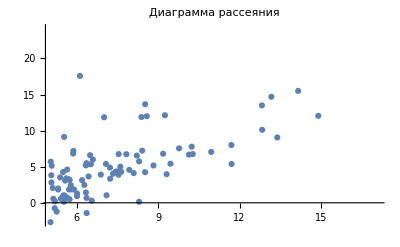

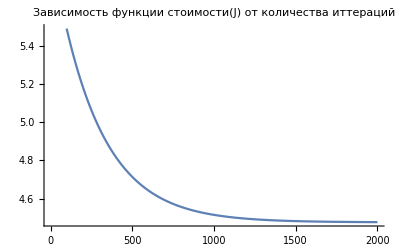

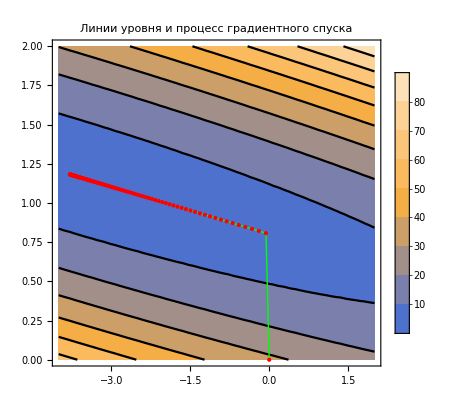

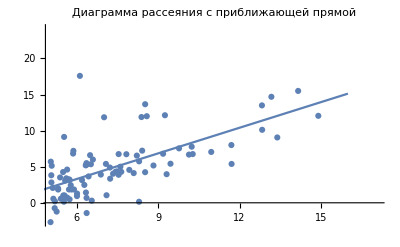

```mathematica
Timing[θ=grad[1/(2Length[X])(X.#-Y)ᵀ.(X.#-Y)&,X,Y,0.01,2000];]
ListPlot[data,ImageSize->400,PlotLabel->"Диаграмма рассеяния"]
ListLinePlot[θ[[2]],ImageSize->400,PlotLabel->"Зависимость функции стоимости(J) от количества иттераций"]
ContourPlot[J[{x1,x2}],{x1,-4,2},{x2,0,2},PlotTheme->"Business",Epilog->{Green,Line[θ[[3]]],Red,Point[θ[[3]]]},ImageSize->400,PlotLabel->"Линии уровня и процесс градиентного спуска"]
Show[ListPlot[data],Plot[{1,x}.θ[[1]],{x,0,16}],ImageSize->400,PlotLabel->"Диаграмма рассеяния с приближающей прямой"]
```

```mathematica
Clear["Global`*"]
```

```mathematica
data={{2104,3,399900},{1600,3,329900},{2400,3,369000},{1416,2,232000},{3000,4,539900},{1985,4,299900},{1534,3,314900},{1427,3,198999},{1380,3,212000},{1494,3,242500},{1940,4,239999},{2000,3,347000},{1890,3,329999},{4478,5,699900},{1268,3,259900},{2300,4,449900},{1320,2,299900},{1236,3,199900},{2609,4,499998},{3031,4,599000},{1767,3,252900},{1888,2,255000},{1604,3,242900},{1962,4,259900},{3890,3,573900},{1100,3,249900},{1458,3,464500},{2526,3,469000},{2200,3,475000},{2637,3,299900},{1839,2,349900},{1000,1,169900},{2040,4,314900},{3137,3,579900},{1811,4,285900},{1437,3,249900},{1239,3,229900},{2132,4,345000},{4215,4,549000},{2162,4,287000},{1664,2,368500},{2238,3,329900},{2567,4,314000},{1200,3,299000},{852,2,179900},{1852,4,299900},{1203,3,239500}};
```

```mathematica
scaling[xx_]:=(xx-Total[data[[;;,1]]]/Length[data])/(Max[data[[;;,1]]]-Min[data[[;;,1]]])
antiscaling[x_]:=InverseFunction[scaling][x]
```

```mathematica
X=Table[{1,scaling[data[[i,1]]],data[[i,2]]},{i,1,Length[data]}]//N;
Y=Table[{data[[i,3]]},{i,1,Length[data]}];
J:=1/(2Length[X])(X.#-Y)ᵀ.(X.#-Y)&
```

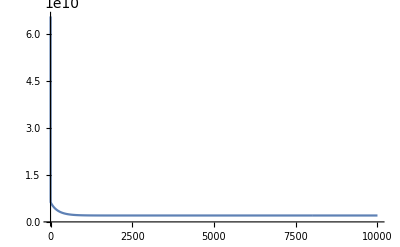

```mathematica
θ=grad[1/(2Length[X])(X.#-Y)ᵀ.(X.#-Y)&,X,Y,0.1,10000];
ListLinePlot[θ[[2]],PlotRange->All]
```

```mathematica
θ1=θ[[1]]
θ2=Inverse[(Xᵀ.X)].Xᵀ.Y
```

{{368114.},{504778.},{-8738.02}}

{{368114.},{504778.},{-8738.02}}

```mathematica
f1[x_,y_]:=θ1ᵀ.{1,scaling[x],y}
f2[x_,y_]:=(θ2ᵀ.{1,scaling[x],y})
```

```mathematica
Show[Plot3D[{f1[x,y],f2[x,y]},{x,1000,5000},{y,2,4}],ListPointPlot3D[data,Filling->Bottom,PlotStyle->{ PointSize[Large]}]]
```

-Graphics3D-

```mathematica
Clear["Global`*"]
```

```mathematica
data=Import["mpg.dat"];
```

```mathematica
XX=Table[Flatten@{1,data[[i,1;;7]]},{i,1,Length[data]}];
Y=Table[{data[[i,8]]},{i,1,Length[data]}];
```

```mathematica
scalled[x_]:=Table[If[i==1,1,(x[[j,i]]-Total[x[[;;,i]]]/Length[x])/(Max[x[[;;,i]]]-Min[x[[;;,i]]])],{j,1,Length[x]},{i,1,Length[x[[1]]]}]
scalle[x_,xx_]:=Table[(x[[i]]-Total[xx[[;;,i+1]]]/Length[xx])/(Max[xx[[;;,i+1]]]-Min[xx[[;;,i+1]]]),{i,1,Length[x]}]
```

```mathematica
X=scalled[XX];
```

```mathematica
J=1/(2Length[X])(X.#-Y)ᵀ.(X.#-Y)&;
```

```mathematica
Timing[θ=grad[J,X,Y,0.1,30000];]
```

$Aborted

```mathematica
N[θ[[1]],10]
```

{{23.4459},{-2.46688},{7.69961},{-3.11901},{-22.834},{1.35367},{9.00927},{2.85228}}

```mathematica
θ2=Inverse[Xᵀ.X].Xᵀ.Y
```

{{23.4459},{-2.46688},{7.69961},{-3.11901},{-22.834},{1.35367},{9.00927},{2.85228}}

```mathematica
h1[x_]:=θ[[1]]ᵀ.Prepend[ x,1]
h2[x_]:=θ2ᵀ.Prepend[ x,1]
```

```mathematica
J[θ[[1]]]
```

{{5.42374}}

```mathematica
J[θ2]
```

{{5.42374}}

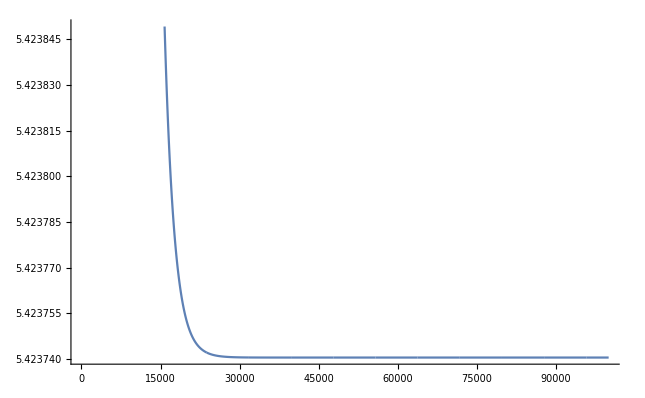

```mathematica
ListLinePlot[θ[[2]]]
```

```mathematica
gradrand[J_,X_,Y_,a_,j_]:=Block[{h,g,i,tt={},m=Length[X],t,θ=Table[0,{g,1,Length@X[[1]]}]},
AppendTo[tt,J[θ]];
For[i=1,i≤j,i++,
g=RandomInteger[{1,Length[X]}];
t=(X.θ-Y);
For[h=1,h≤Length@X[[1]],h++,θ[[h]]=θ[[h]]-a 1/m t[[g]]X[[g,h]];];
AppendTo[tt,J[θ]];];
{θ,Flatten@tt}]
```

```mathematica
Timing[θ3=gradrand[J,X,Y,0.5,300000];]
```

{778.422,Null}

```mathematica
θ[[1]]
```

{{23.4459},{-2.46688},{7.69961},{-3.11901},{-22.834},{1.35367},{9.00927},{2.85228}}

```mathematica
θ3[[1]]
```

{{23.4686},{-1.18694},{2.70056},{-4.31594},{-18.8133},{-0.437827},{8.85015},{2.70876}}

```mathematica
J[ θ3[[1]] ]
```

{{5.48788}}

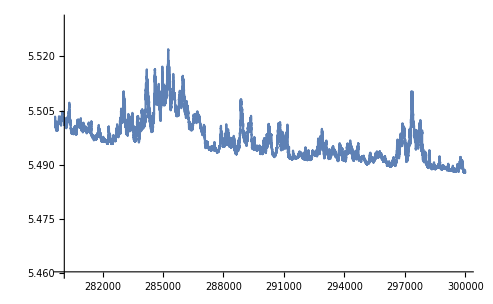

```mathematica
ListLinePlot[θ3[[2]],PlotRange->{{280000,300000},{5.46,5.53}}]
```